### Pregunta 1

#### Parte a

```mathematica
(I+I^2+I^3+I^4+I^5+I^6)/(2+3I)
```

1/13+(5 ⅈ)/13

#### Parte b

```mathematica
z1 = 3 I; z2 = 2+2I;
```

```mathematica
NSolve[w^3==Conjugate[z1]z2,w]
```

{{w→-1.44225-1.44225 ⅈ},{w→-0.5279+1.97015 ⅈ},{w→1.97015-0.5279 ⅈ}}

```mathematica
(*Nuestros resultados son*)
```

```mathematica
Table[N[72^(1/6)Exp[(-I Pi)/12+(I 2 k Pi)/3]],{k,0,2}]
```

{1.97015-0.5279 ⅈ,-0.5279+1.97015 ⅈ,-1.44225-1.44225 ⅈ}

```mathematica
(*Son los mismos resultados, Solo cambia la posicion del ultimo y primer resultado, pero es lo mismo*)
```

```mathematica
(*Dibujando los resultados, de aqui se puede ver que el resultado numerico tiene el radio obtenido, ya que los 3 vectores acaban en la circunferencia*)
```

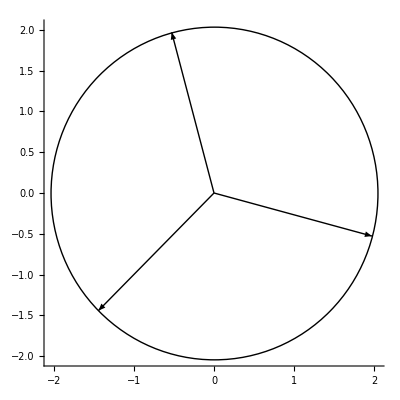

```mathematica
Graphics[{Arrow[{{0,0},{-1.44225,-1.44225}} ],Arrow[{{0,0},{-0.5279, 1.97015}}],Arrow[{{0,0},{1.97015,-0.5279}}],,Circle[{0,0},72^(1/6)]} ,Axes->True]
```

### Pregunta 2

```mathematica
Integrate[x^2/(x^4+1),{x,0,Infinity}]
```

π/(2 √2)

### Pregunta 4

#### Parte a

```mathematica
path4a[t_]:=4 Exp[I t]
```

```mathematica
f4a[z_]:= Sin[z]/Sinh[z]
```

```mathematica
Residue[f4a[z],{z,0}]
```

0

```mathematica
{Residue[f4a[z],{z,-2 Pi I}],Sin[-2 Pi I]/Cosh[-2 Pi I]}
```

{-ⅈ Sinh[2 π],-ⅈ Sinh[2 π]}

```mathematica
{Residue[f4a[z],{z,2 Pi I}],Sin[2 Pi I]/Cosh[2 Pi I]}
```

{ⅈ Sinh[2 π],ⅈ Sinh[2 π]}

```mathematica
(*Son iguales con signo contrario, se cancelan y suman 0*)
```

```mathematica
(*Comprobacion numerica*)
```

```mathematica
NIntegrate[f4a[path4a[t]]path4a'[t],{t,0,2Pi}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.6632}. NIntegrate obtained 1.86517×10^-14+2.10942×10^-15 ⅈ and 3.5918×10^-14 for the integral and error estimates.

1.86517×10^-14+2.10942×10^-15 ⅈ

```mathematica
(*Advertencia de que oscila convergiendo, pero convergiendo a 0, todo bien*)
```

#### Parte b

```mathematica
path4b[t_]:=Exp[I t]
```

```mathematica
f4b[z_]:= 1/(z Sin[z]ArcTan[z])
```

```mathematica
NIntegrate[f4b[path4b[t]]path4b'[t],{t,0,2Pi}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.58297}. NIntegrate obtained -4.34982×10^-16+3.14159 ⅈ and 0.0000137954 for the integral and error estimates.

-4.34982×10^-16+3.14159 ⅈ

### Pregunta 5

#### Parte a

```mathematica
Simplify[Sin[2 n Pi + Pi/2-I *(Cosh[4]+√(Cosh[4]^2-1))],Element[n,Integers]]
```

Cosh[ⅇ^4]

```mathematica
(*La respuesta si da evaluando lo obtenido*)
```

#### Parte b

```mathematica
Simplify[Cos[2 k Pi - I Log[2+√3]],Element[k,Integers]]
```

2